TTTval = 1, N[TTTval] = 1.

c1 = 2, c2 = 4, c3 = 2, c4 = 4, c5 = 2

c1 = 2., c2 = 4., c3 = 2., c4 = 4., c5 = 2.

TTT

c1Val = 3-TTT, c2Val = 3+TTT^2, c3Val = 3-TTT^3, c4Val = 3+TTT^4, c5Val = 3-TTT^5

FindMinimum

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 2000 iterations.

sol[[1]] = 1.48412×10^-29

xLstSolSorted = {-1.,-4.0293×10^-9,-3.40421×10^-9,-3.39189×10^-9,-3.35854×10^-9,-2.95988×10^-9,-2.76601×10^-9,-2.76016×10^-9,-2.14632×10^-9,-2.11275×10^-9,-2.10806×10^-9,-2.01804×10^-9,-1.98437×10^-9,-1.95587×10^-9,-1.93586×10^-9,-1.92082×10^-9,-1.90718×10^-9,-1.89525×10^-9,-1.37116×10^-9,-1.25456×10^-9,-1.19754×10^-9,-1.04025×10^-9,-1.00881×10^-9,-9.65152×10^-10,-6.00281×10^-10,-1.86082×10^-10,5.36527×10^-11,6.03171×10^-11,6.50512×10^-11,1.22221×10^-10,8.90582×10^-10,8.90819×10^-10,1.79214×10^-9,1.8012×10^-9,2.49935×10^-9,2.52599×10^-9,2.58315×10^-9,2.67396×10^-9,2.69827×10^-9,2.71154×10^-9,2.7153×10^-9,2.71544×10^-9,3.01464×10^-9,4.16278×10^-9,4.33239×10^-9,5.95452×10^-9,6.01503×10^-9,1.,1.,1.}

M1 = 2., M2 = 4., M3 = 2., M4 = 4., M5 = 2., (M3*M2/M5)*(c5/(c3*c2)) = 1., (M4/M2^2)*(c2^2/c4) = 1.

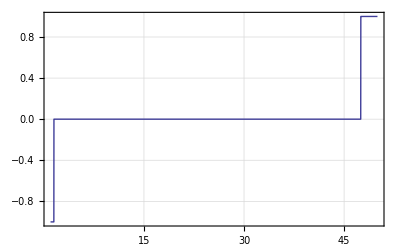

```mathematica
NoOfElements=50;
TTTval=3^(1/5);
TTTval=1000/1000;
Print["TTTval = ", TTTval, ", N[TTTval] = ", N[TTTval]];

plotOpts ={PlotRange -> All, PlotStyle -> Thick, Frame -> True, GridLines -> Automatic};

Moment[lst_?VectorQ,level_?IntegerQ]:=Module[{len,ii,retVal},
len=Length[lst];
retVal=Sum[lst[[ii]]^level,{ii,1,len}];
Return[retVal];
];

cFunc[level_?IntegerQ,ns_?IntegerQ,nt_?IntegerQ,ttt_]:=(ns+nt*(-ttt)^level);
cFunc31[level_?IntegerQ,ttt_]:=cFunc[level,3,1,ttt];
cFunc13[level_?IntegerQ,ttt_]:=cFunc[level,1,3,ttt];
(*
Print["..."];
Expand[cFunc31[3,TTT]*cFunc31[5,TTT]-0*cFunc31[4,TTT]^2]

tttMin=2;
tttMax=3.1;

Print[Plot[cFunc31[1,ttt],{ttt,0,tttMax},Evaluate[plotOpts]]];
Print[Plot[cFunc31[2,ttt],{ttt,0,tttMax},Evaluate[plotOpts]]];
Print[Plot[cFunc31[3,ttt],{ttt,0,tttMax},Evaluate[plotOpts]]];
Print[Plot[cFunc31[4,ttt],{ttt,0,tttMax},Evaluate[plotOpts]]];
Print[Plot[cFunc31[5,ttt],{ttt,0,tttMax},Evaluate[plotOpts]]];

Print["c2*c3/c5"];
Print[Plot[cFunc31[2,ttt]*cFunc31[3,ttt]/cFunc31[5,ttt],{ttt,tttMin,tttMax},Evaluate[plotOpts]]];

Print["c4/c2^2"];
Print[Plot[cFunc31[4,ttt]/cFunc31[2,ttt]^2,{ttt,tttMin,tttMax},Evaluate[plotOpts]]];

Print["c3*c5/c2^4"];
Print[Plot[cFunc31[5,ttt]*cFunc31[3,ttt]/cFunc31[2,ttt]^4,{ttt,tttMin,tttMax},Evaluate[plotOpts]]];
*)

IndexedFunc[lst_?VectorQ,idxVal_?NumericQ]:=Module[{len,idx},
len=Length[lst];
idx=Max[Min[Round[Re[idxVal]],len],1];
Return[lst[[idx]]];
];

(*
lstFunc[lst_?VectorQ]:=Module[{len,ii,retVal},
len=Length[lst];
retVal=Sum[lst[[ii]]^2,{ii,1,len}];
Return[retVal];
];
*)

c1=cFunc31[1,TTTval];
c2=cFunc31[2,TTTval];
c3=cFunc31[3,TTTval];
c4=cFunc31[4,TTTval];
c5=cFunc31[5,TTTval];
Print["c1 = ", c1, ", c2 = ", c2, ", c3 = ", c3, ", c4 = ", c4, ", c5 = ", c5];
Print["c1 = ", N[c1], ", c2 = ", N[c2], ", c3 = ", N[c3], ", c4 = ", N[c4], ", c5 = ", N[c5]];


c1Val=cFunc31[1,TTT];
c2Val=cFunc31[2,TTT];
c3Val=cFunc31[3,TTT];
c4Val=cFunc31[4,TTT];
c5Val=cFunc31[5,TTT];

Expand[(((c2Val-c1Val^2)/6)+1)]

Print["c1Val = ", c1Val, ", c2Val = ", c2Val, ", c3Val = ", c3Val, ", c4Val = ", c4Val, ", c5Val = ", c5Val];


a532=1;
a5221=1;
a422=1;
a211=1;
a2=1;

a541=0;
a5311=0;
a52111=0;
a511111=0;

m541Func[lst_?VectorQ]:=Module[{retVal,M1,M2,M3,M4,M5},
M1=Moment[lst,1];
M2=Moment[lst,2];
M3=Moment[lst,3];
M4=Moment[lst,4];
M5=Moment[lst,5];
retVal=0;
Return[retVal];
];

lstFunc[lst_?VectorQ]:=Module[{len,ii,retVal,M1,M2,M3,M4,M5,m541,m532,m5311,m5221,m52111,m511111,m2,m422,m211},
M1=Moment[lst,1];
M2=Moment[lst,2];
M3=Moment[lst,3];
M4=Moment[lst,4];
M5=Moment[lst,5];

m532=a532*(c3*c2*M5-c5*M3*M2)^2;
m5221=a5221*(c2^2*c1*M5-c5*M2^2*M1)^2;
m422=a422*M2*(c2^2*M4-c4*M2^2)^2;
m211=a211*M2^3*(c1^2*M2-c2*M1^2)^2;
m2=a2*(M2-c2)^2;

m541=a541*(c4*c1*M5-c5*M4*M1)^2;
m5311=a5311*(c3*c1^2*M5-c5*M3*M1^2)^2;
m52111=a52111*(c2*c1^3*M5-c5*M2*M1^3)^2;
m511111=a511111*(c1^5*M5-c5*M1^5)^2;

retVal=m541+m532+m5311+m5311+m5221+m52111+m511111+m422+m211+m2;
Return[retVal];
];

initValLst=Table[RandomReal[NormalDistribution[]],{ii,1,NoOfElements}];

Print["FindMinimum"];
sol=FindMinimum[lstFunc[xLst],{xLst,initValLst},WorkingPrecision -> 200, MaxIterations -> 2000];
xLstSol=xLst /. sol[[2]];
xLstSolSorted=Sort[xLstSol];
Print["sol[[1]] = ", N[sol[[1]]]];
(* Print["xLstSol = ", N[xLstSol]]; *)
Print["xLstSolSorted = ", N[xLstSolSorted]];
M1=Moment[xLstSol,1];
M2=Moment[xLstSol,2];
M3=Moment[xLstSol,3];
M4=Moment[xLstSol,4];
M5=Moment[xLstSol,5];

Print["M1 = ", N[M1], ", M2 = ", N[M2],", M3 = ", N[M3],", M4 = ", N[M4],", M5 = ", N[M5], ", (M3*M2/M5)*(c5/(c3*c2)) = ", N[(M3*M2/M5)*(c5/(c3*c2))],", (M4/M2^2)*(c2^2/c4) = ", N[(M4/M2^2)*(c2^2/c4)]];

Print[Plot[IndexedFunc[xLstSolSorted,idx],{idx,1,NoOfElements},Evaluate[plotOpts]]];
```